```mathematica
$Assumptions={a>0&&c>=0&&Γ>0}
```

{a>0&&c≥0&&Γ>0}

```mathematica
PrependTo[$Path,NotebookDirectory[]];
<< "GaussianPiecewiseIntegrals`"
IntInf[f_,intvar_:x]:=GaussianIntegral[f,intvar]
```

```mathematica
Theta[x]:=Piecewise[{{1,x>0}},0];
```

```mathematica
Klinear[f_]:=a x f + Γ D[f,x]
Kcubic[f_]:=(a x+c x^3) f + Γ D[f,x]
Kcubicnegative[f_]:=(-a x+c x^3) f + Γ D[f,x]
Ktheta[f_]:=(a x-c(1/2-Theta[x]))f+Γ D[f,x];
```

```mathematica
linear = DSolveValue[Klinear[P[x]]==0,P[x],x];
linear=linear/IntInf[linear]
cubic = DSolveValue[Kcubic[P[x]]==0,P[x],x];
cubic=cubic/Integrate[cubic,{x,-Infinity,Infinity}]
negativecubic = DSolveValue[Kcubicnegative[P[x]]==0,P[x],x];
negativecubic=negativecubic/Integrate[negativecubic,{x,-Infinity,Infinity}]
theta = DSolveValue[Ktheta[P[x]]==0,P[x],x];
theta=theta/Integrate[theta,{x,-Infinity,Infinity}]
```

(ⅇ^(-(a x^2)/(2 Γ)) √(a/Γ))/(√(2 π))

(√2 ⅇ^(-a^2/(8 c Γ)-((a x^2)/2+(c x^4)/4)/Γ))/(√(a/c) BesselK[1/4,a^2/(8 c Γ)])

(2 ⅇ^(-a^2/(8 c Γ)+((a x^2)/2-(c x^4)/4)/Γ))/(√(a/c) π (BesselI[-1/4,a^2/(8 c Γ)]+BesselI[1/4,a^2/(8 c Γ)]))

(ⅇ^(-c^2/(8 a Γ)+(Piecewise[{{(c x-a x^2)/(2 Γ), x≤0}, {-(c x+a x^2)/(2 Γ), True}}])) √(a Γ))/(√(2 π) Γ Erfc[c/(2 √2 √(a Γ))])

```mathematica
lettertable=Table[Graphics[Style[Text["("<>(Alphabet[][[i]])<>")",Scaled[{0.1,0.9}]],FontSize->15]],{i,1,4}];
GenFigure[equation_,legend_,letter_]:=Module[{},
Show[{Plot[equation,{x,-5,5},PlotLabel->legend,LabelStyle->{FontSize->14},PlotRange->{0,0.6},ImagePadding->10,PlotRangePadding->0.05],letter},ImageSize->All]
]
```

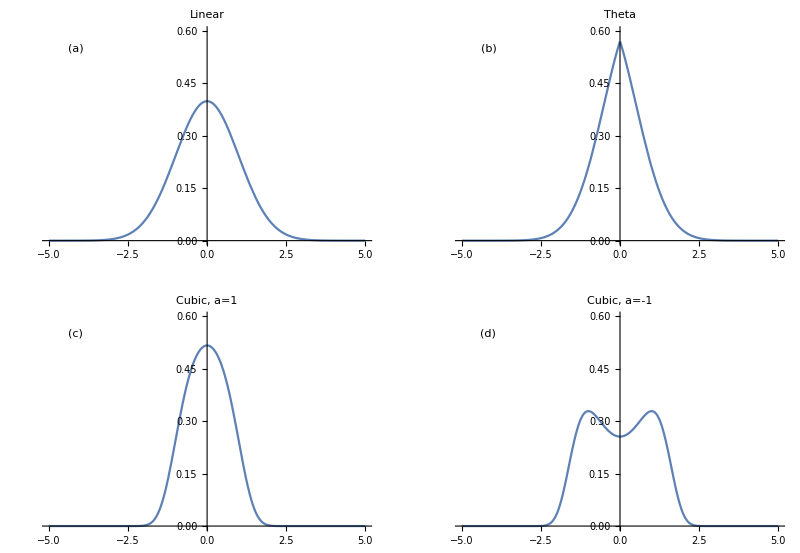

```mathematica
params={a->1,c->1,Γ->1};
plots={{GenFigure[linear/.params,"Linear",lettertable[[1]]],GenFigure[theta/.params,"Theta",lettertable[[2]]]},{GenFigure[cubic/.params,"Cubic, a=1",lettertable[[3]]],GenFigure[negativecubic/.params,"Cubic, a=-1",lettertable[[4]]]}};
plotsoutput=GraphicsGrid[plots,Spacings->Scaled[0.1],ImageMargins->15]
```

```mathematica
Export[NotebookDirectory[]<>"Images\\Exact Solutions.png",plotsoutput,"PNG"]
```

C:\Users\ethan\OneDrive\Documents\Wolfram Mathematica\Final versions for thesis\Images\Exact Solutions.png